```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_, m_]:=(1-Cos[Pi*(x+m-0.5)])/2;
```

```mathematica
Manipulate[Plot[f[x,m],{x,0,2 Pi}],{m,0,1}]
```

```mathematica
df[x_]:=D[f[x],x]
```

```mathematica
p0x
```

p0x

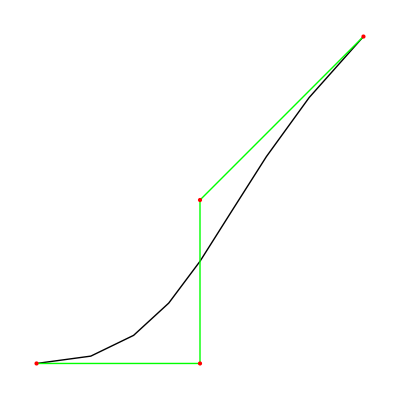

```mathematica
pts={{0,0},{0.5,0},{0.5,0.5},{1,1}};
Graphics[{BezierCurve[pts],Green,Line[pts],Red,Point[pts]}]
```

```mathematica
p0[x_,y_]:={x,y};
p1[x_,y_]:={x,y};
p2[x_,y_]:={x,y};
p3[x_,y_]:={x,y};
B[t_,a_,b_,c_]:=p0[0,0]*(1-t)^3+3*p1[a,Boole[c<0.5]*(1+Cos[2*Pi*c])/2]*t*(1-t)^2+3*p2[b,Boole[c<0.5]+Boole[c>=0.5]*(1-Cos[2*Pi*c])/2]*t^2*(1-t)+p3[1,1]*t^3;
```

```mathematica
Manipulate[ParametricPlot[B[t,a,b,c],{t,0,1}],{a,0,1},{b,0,1},{c,0,1}]
```

```mathematica
fx[x_]:=Part[B[t,a,b,c],1]
fy[y_]:=Part[B[t,a,b,c],2]
```

```mathematica
fx[x]
```

3 a (1-t)^2 t+3 b (1-t) t^2+t^3

```mathematica
fy[y]
```

t^3+3 (1-t) t^2 (Boole[c<0.5]+1/2 Boole[c≥0.5] (1-Cos[2 c π]))+3/2 (1-t)^2 t Boole[c<0.5] (1+Cos[2 c π])

```mathematica
B[t,a,b,c]
```

{3*a*(1 - t)^2*t + 3*b*(1 - t)*t^2 + t^3, t^3 + 3*(1 - t)*t^2*(Boole[c < 0.5] + (1/2)*Boole[c >= 0.5]*(1 - Cos[2*c*Pi])) + 
   (3/2)*(1 - t)^2*t*Boole[c < 0.5]*(1 + Cos[2*c*Pi])}

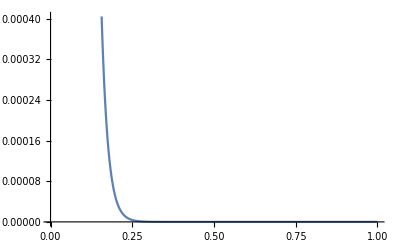

```mathematica
Plot[Exp[-50*x],{x,0,1}]
```

```mathematica
dfx=D[fx[x],t]
```

3 a (1-t)^2-6 a (1-t) t+6 b (1-t) t+3 t^2-3 b t^2

```mathematica
Factor[dfx]
```

3 (a-4 a t+2 b t+t^2+3 a t^2-3 b t^2)

```mathematica
tm[x_,psi_]:=Log[x*(psi-1)+1]/Log[psi];
```

```mathematica
Manipulate[Plot[tm[x,psi],{x,0,1}],{psi,0,10}]
```

```mathematica
D[B[t,a,b,c],a]
```

{3 (1-t)^2 t,0}